For the MinMax Graphon we need some assumptions to solve the integrals properly

```mathematica
$Assumptions=a>0 && b<1 && a<b &&  a<1 && b>0&&x>0 && x< 1 && y>0 && y<1
```

a>0&&b<1&&a<b&&a<1&&b>0&&x>0&&x<1&&y>0&&y<1

```mathematica
graphon[x_,y_] = Min[x,y]*(1 -Max[x,y])
```

(1-Max[x,y]) Min[x,y]

Modularity surface

```mathematica
BM[x_,y_] = graphon[x,y] - 3*x*y(1-x)(1-y)
```

-3 (1-x) x (1-y) y+(1-Max[x,y]) Min[x,y]

Modularity slice

```mathematica
L[a_,b_]=Simplify[Integrate[Integrate[Min[x,y]*(1 -Max[x,y])  - 3*x*y(1-x)(1-y) ,{y,a,b}],{x,a,b}]]
```

1/3 (-3 a^4+3 a^5-a^6-3 a^2 (-1+b)^2 b-(-1+b)^3 b^3+a^3 (2-3 b^2+2 b^3))

For three communities the modularity is proportional to the following function. The free parameters are the positions of the borders x1 and x2. We obtain

```mathematica
Q = L[0,x1] + L[x1,x2]+L[x2,1]
```

-1/3 (-1+x1)^3 x1^3+1/3 (x2^3-3 x2^4+3 x2^5-x2^6)+1/3 (-3 x1^4+3 x1^5-x1^6-3 x1^2 (-1+x2)^2 x2-(-1+x2)^3 x2^3+x1^3 (2-3 x2^2+2 x2^3))

The modularity maximisation can then be solved with a two-dimensional optimisation procedure.

```mathematica
Maximize[{Q,x1>0 && x2<1 && x1<x2},{x1,x2}]
```

{-4/27 (-7+4 √3),{x1→Root0.423Root[{16+1512 #1+729 #1^2&,-8476672-796937472 #1-516096 #2^2-48522240 #1 #2^2+14395392 #2^3+1353397248 #1 #2^3-28281600 #2^4-2658925440 #1 #2^4+27396864 #2^5+2576064384 #1 #2^5-18764160 #2^6-1766905488 #1 #2^6+37366272 #2^7+3522609648 #1 #2^7-69807744 #2^8-6604468812 #1 #2^8+78208416 #2^9+7633399824 #1 #2^9-56858112 #2^10-6594382368 #1 #2^10+25468344 #2^11+6315644844 #1 #2^11+56055240 #2^12-8105032935 #1 #2^12-454703544 #2^13+9543971772 #1 #2^13+1717853508 #2^14-8280323172 #1 #2^14-4235383566 #2^15+5054594400 #1 #2^15+7430371866 #2^16-2071911312 #1 #2^16-9675808506 #2^17+510183360 #1 #2^17+9560544858 #2^18-56687040 #1 #2^18-7217204976 #2^19+4124454552 #2^20-1732733856 #2^21+504514656 #2^22-90699264 #2^23+7558272 #2^24&},{2,3}]0.4226497308103742,x2→Root0.577Root[{16+1512 #1+729 #1^2&,-8476672-796937472 #1-516096 #2^2-48522240 #1 #2^2+14395392 #2^3+1353397248 #1 #2^3-28281600 #2^4-2658925440 #1 #2^4+27396864 #2^5+2576064384 #1 #2^5-18764160 #2^6-1766905488 #1 #2^6+37366272 #2^7+3522609648 #1 #2^7-69807744 #2^8-6604468812 #1 #2^8+78208416 #2^9+7633399824 #1 #2^9-56858112 #2^10-6594382368 #1 #2^10+25468344 #2^11+6315644844 #1 #2^11+56055240 #2^12-8105032935 #1 #2^12-454703544 #2^13+9543971772 #1 #2^13+1717853508 #2^14-8280323172 #1 #2^14-4235383566 #2^15+5054594400 #1 #2^15+7430371866 #2^16-2071911312 #1 #2^16-9675808506 #2^17+510183360 #1 #2^17+9560544858 #2^18-56687040 #1 #2^18-7217204976 #2^19+4124454552 #2^20-1732733856 #2^21+504514656 #2^22-90699264 #2^23+7558272 #2^24&,-3 #1-3 #2^3+6 #2^4-6 #2^5+2 #2^6+3 #2^2 #3-6 #2^2 #3^2+3 #2^3 #3^2-2 #3^3+3 #2^2 #3^3-2 #2^3 #3^3+6 #3^4-6 #3^5+2 #3^6&},{2,3,4}]0.5773502691896257}}

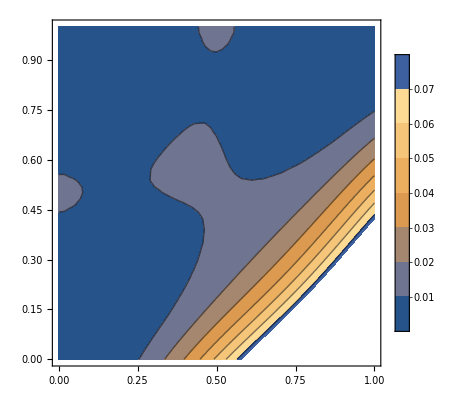

```mathematica
ContourPlot[Q,{x1,0,1},{x2,0,1},PlotLegends->Automatic]
```